# Modulation Instability Aug.25

Stability. Otherwise, instability.

## -plane contour plots

```mathematica
f[k_,α_,N_]:=Sum[Sin[k*m/2]^2/m^(1+α),{m,1,N}]
```

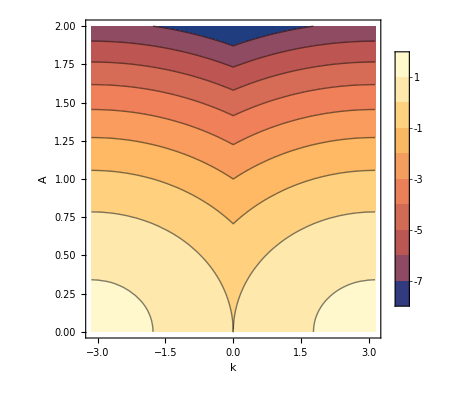

```mathematica
ContourPlot[(f[k,α,1000]- 2 A^2)/.{α->1},{k,-π,π}, {A,0,2},FrameLabel->{"k","A"},PlotLegends->Automatic]
```

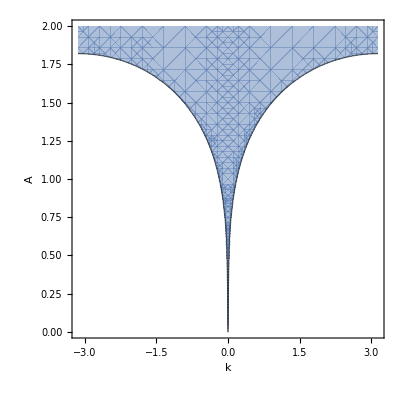

```mathematica
ContourPlot[(4f[k,0.5,1000]-2 A^2),{k,-π,π},{A,0,2},FrameLabel->{Style["k",16,Bold],Rotate[Style["A",16,Bold], -90 Degree]},FrameStyle->Thick,PlotLegends->Automatic,Contours->{0},ContourShading->{{Opacity[.5],ColorData[97][1]},None}]
```

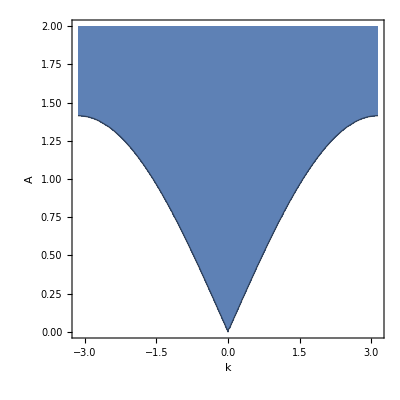

```mathematica
ContourPlot[(4f[k,50,1000]-2 A^2),{k,-π,π},{A,0,2},FrameLabel->{Style["k",16,Bold],Rotate[Style["A",16,Bold], -90 Degree]},FrameStyle->Thick,PlotLegends->Automatic,Contours->{0},ContourShading->{{ColorData[97][1]},None}]
```

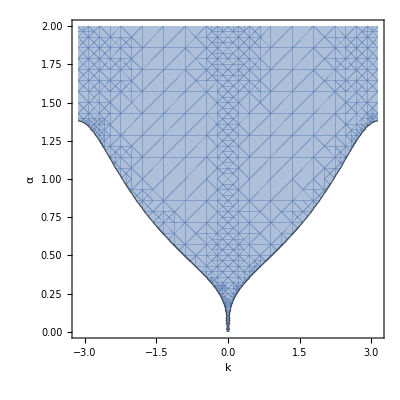

```mathematica
ContourPlot[(4f[k,α,1000]-2 (A)^2)/.A->1.5,{k,-π,π},{α,0,2},FrameLabel->{Style["k",16,Bold],Style["α",16,Bold]},FrameStyle->Thick,PlotLegends->Automatic,Contours->{0},ContourShading->{{Opacity[.5],ColorData[97][1]},None}]
```